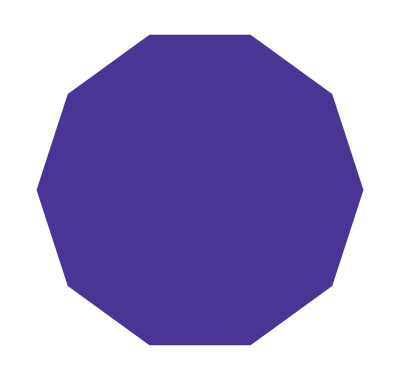
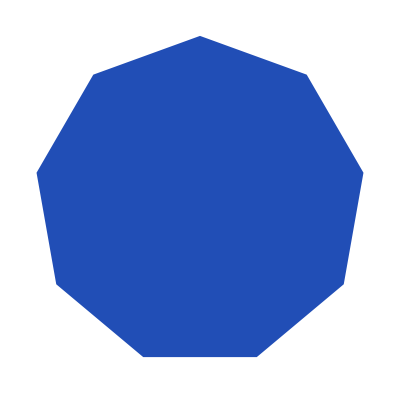
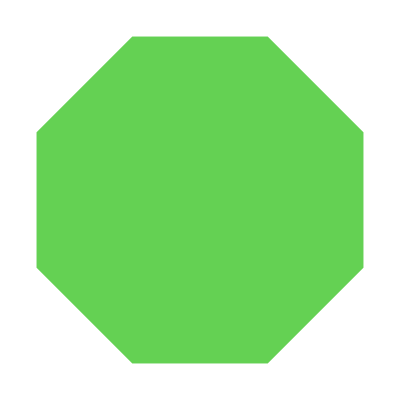
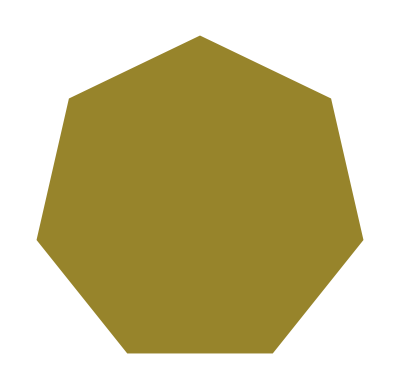
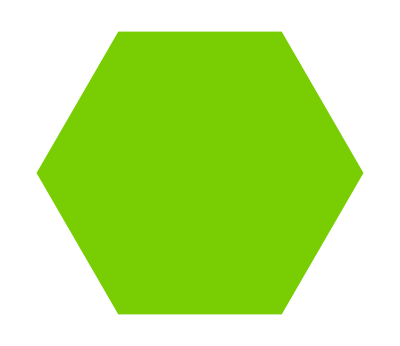
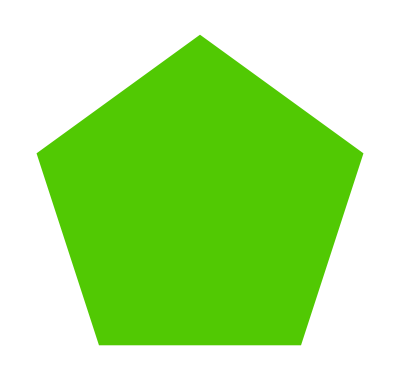
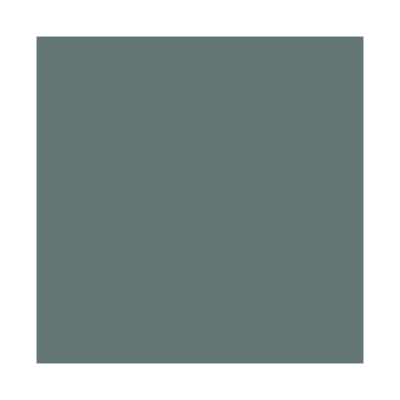
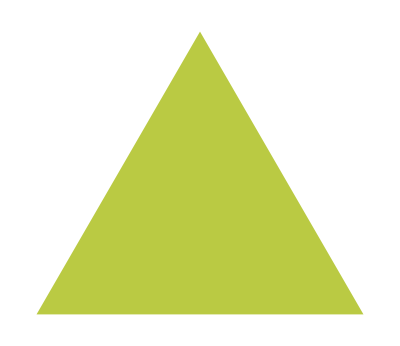

```mathematica
(* Ogetti grafici *)
(* Ci sono delle direttive che definiscono gli oggetti che poi vengono disegnati tramite la direttiva Graphics *)
(* Roba che altera colore/opacità e tutte cose devono essere inserite prima dell'oggetto grafico che deve subire quelle modifiche *)
(* Module: in mezzo c'ha una serie di operazioni, vedi sul libro cosa fa perchè la spiegata un po' a cazzo di cane
1. Lista di variabili private alla module che poi nel package non saranno note al notebook, l'area di dichiarazione è anche eventuale area di inizializzazione
Andare a capo o mettere uno spazio all'interno della module viene visto come una moltiplicazione quindi ogni statement deve essere chiuso con un ;
Dato che alcuni valori devono essere passati in input dall'utente alcune variabili dovranno essere settate dinamicamente e quindi esiste la dynamic module*)
(*preincrement: fa la add e restituisce il valore nuovo
increment: fa la add e restituisce il valore vecchio*)
(*reap e sow sono come i carabinieri che vanno sempre in coppia, che sono meglio di part e flatten perchè part e flatten funzionano coi grafici solo con l'implementazione corrente*)
(* 8.8 *)
SeedRandom[1];
Graphics[Table[Style[RegularPolygon[k],RandomColor[]],{k,8,3,-1}]];
(* +8.3 *)
Table[Graphics[Style[RegularPolygon[k], RandomColor[]], ImageSize->Tiny], {k, 10, 3, -1}]
```